```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]=(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)
g[x_]=A*UnitBox[x/b]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

A UnitBox[x/b]

```mathematica
c[y_]=Assuming[b>0,Convolve[g[x],f[x],x,y]]
```

1/2 A (Erf[(b+2 y-2 μ)/(2 √2 σ)]+Erf[(b-2 y+2 μ)/(2 √2 σ)])

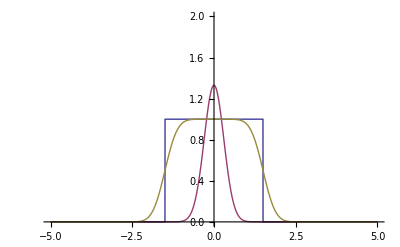

```mathematica
l={μ->0,σ->0.3,b->3,A->1};
Plot[{g[x]/.l,f[x]/.l,c[x]/.l},{x,-5,5},PlotRange->{0,2}]
```